# 14-structure S-band linac: distributed matching and FODO

Edit the inputs in Section 1, then choose Evaluation > Evaluate Notebook. Example Twiss values are placeholders. Input plane: entrance of Q1 between S1 and S2, s=3.357 m. Q1-Q4 match to the thick-lens magnetic FODO reference at Q5 entrance. Q5-Q13 have constant alternating normalized k and energy-scaled gradients. 70 degrees refers to the full 8.06 m reference cell; actual accelerating optics are not strictly periodic. Upstream of Q1 the plotted optics are inferred by inverse transport. Outputs go to Sband14_output beside this notebook.

## 1. Inputs: evaluate the complete file after changing this section

```mathematica
ClearAll["Global`*"];(*alphaXIn=-0.1339;alphaYIn=-1.6034;betaXIn=15.20938;betaYIn=3.225642;*)
alphaXIn=0.1297;alphaYIn=-0.6370;betaXIn=11.278931;betaYIn=1.702012;
energyAtQ1MeV=66.57;emitNxMMmrad=43.;emitNyMMmrad=26.5;firstStructureGainMeV=39.24;subsequentGainMeV=53.;rfPhaseDeg=0.;phasePerFullCellDeg=70.;structureLength=3.008;cavityExrLength=0.072;quadLength=0.25;correctorLength=0.1;bellowOutLength=0.076;bpmLength=0.101;pumpScreenLength=0.125;ictLength=0.075;valveLength=0.072;bellowInLength=0.076;spoolLength=0.075;gapLength=bellowOutLength+correctorLength+bpmLength+quadLength+pumpScreenLength+ictLength+valveLength+spoolLength+bellowInLength;ordinarySpoolLength=spoolLength+ictLength+valveLength;maxMatchingGradientTm=10.;matchTolerance=1/10^6;numberOfStarts=24;randomSeed=14095;nRF=60;nQuad=12;nDrift=4;outputDirectory=If[StringQ[$InputFileName]&&StringLength[$InputFileName]>0,FileNameJoin[{DirectoryName[$InputFileName],"Sband14_output"}],FileNameJoin[{NotebookDirectory[],"Sband14_output"}]];
```

## 2. Conventions and transport matrices

```mathematica
(* x,x' and y,y'. k [m^-2] > 0 focuses x. kL [m^-1]. G=k B rho [T/m].
   The sign of physical pole wiring for electrons must follow the magnet convention.
   RF matrix copied algebraically from FODO_vs_Triplet.nb (ultrarelativistic).
   It has determinant gamma_i/gamma_f, not the exact p_i/p_f.
   Covariances are transported directly; emittance is NOT reset at each element.
   This is an uncoupled linear on-momentum model, without wakes or space charge. *)
me = 0.51099895;
gam[e_] := 1. + e/me;
mom[e_] := Sqrt[e (e + 2 me)];
brho[e_] := mom[e]/299.792458;
drift[l_] := {{1., l}, {0., 1.}};
quad[k_?NumericQ, l_?NumericQ] := Which[Abs[k] < 10^-14, drift[l],
 k > 0, With[{v = Sqrt[k]}, {{Cos[v l], Sin[v l]/v}, {-v Sin[v l], Cos[v l]}}],
 True, With[{v = Sqrt[-k]}, {{Cosh[v l], Sinh[v l]/v}, {v Sinh[v l], Cosh[v l]}}]];
rf[ei_, ef_, l_] := Module[{gi = gam[ei], gf = gam[ef], c = Cos[rfPhaseDeg Degree], gp, a},
 If[Abs[ef-ei] < 10^-12, Return[drift[l]]];
 gp = (gf-gi)/(l c); a = Log[gf/gi]/(Sqrt[8.] c);
 {{Cos[a]-Sqrt[2.] c Sin[a], Sqrt[8.] gi/gp c Sin[a]},
 {-(gp/gf) (c/Sqrt[2.] + 1/(Sqrt[8.] c)) Sin[a], gi/gf (Cos[a]+Sqrt[2.] c Sin[a])}}];
(* Cumulative entrance-to-z map. Remove the fictitious exit edge at interior
   points; use full cavity map only at the physical exit. Never concatenate
   full-cavity matrices for artificial slices. Entrance edge appears at z=0+. *)
rfPartial[ei_, ef_, l_, z_] := Module[{ez, rate, exit},
 If[z <= 0, Return[IdentityMatrix[2]]];
 If[z >= l-10^-12, Return[rf[ei, ef, l]]];
 ez = ei + (ef-ei) z/l; rate = (gam[ef]-gam[ei])/l;
 exit = {{1., 0.}, {rate/(2 gam[ez]), 1.}};
 Inverse[exit].rf[ei, ez, z]];
twissMatrix[b_, a_] := {{b, -a}, {-a, (1+a^2)/b}};
unitTwiss[s_] := s/Sqrt[Det[s]];
transport[m_, s_] := m.s.Transpose[m];
assert[condition_, message_] := If[!TrueQ[condition], Print["ERROR: ", message]; Abort[]];
assert[Min[betaXIn, betaYIn, emitNxMMmrad, emitNyMMmrad, energyAtQ1MeV-firstStructureGainMeV] > 0,
 "Positive beta, emittance and S1 entrance energy required."];
assert[0 < phasePerFullCellDeg < 175 && Abs[Cos[rfPhaseDeg Degree]] > 10^-6,
 "Invalid reference phase or RF phase."];
assert[subsequentGainMeV >= 0 && firstStructureGainMeV >= 0 && maxMatchingGradientTm > 0,
 "Use nonnegative gains and positive gradient bound."];
```

## 3. Full physical lattice: s=0 at S1 entrance, all 14 structures

```mathematica
lattice = {}; position = 0.; energy = energyAtQ1MeV-firstStructureGainMeV;
add[name_, type_, length_, index_:0, gain_:0.] := Module[{},
 AppendTo[lattice, <|"Name"->name, "Type"->type, "Index"->index,
 "sStart_m"->position, "sEnd_m"->position+length, "Length_m"->length,
 "Kin_MeV"->energy, "Kout_MeV"->energy+gain|>]; position += length; energy += gain;];
Do[
 add["S"<>ToString[j], "RF", structureLength, j, If[j==1, firstStructureGainMeV, subsequentGainMeV]];
 (* Passive cavity drift/flange after EVERY RF structure, including S14. *)
 add["CavityExt"<>ToString[j], "CavityExt", cavityExrLength];
 If[j < 14,
  add["BellowOut"<>ToString[j], "Drift", bellowOutLength];
  add["Corrector"<>ToString[j], "Corrector", correctorLength];
  add["BPM"<>ToString[j], "BPM", bpmLength];
  add["Q"<>ToString[j], "Quad", quadLength, j];
  add["PumpScreen"<>ToString[j], "ScreenPump", pumpScreenLength];
  If[EvenQ[j], add["ICT"<>ToString[j], "ICT", ictLength]; add["Valve"<>ToString[j], "Valve", valveLength]];
  spool = If[EvenQ[j], spoolLength, ordinarySpoolLength];
  assert[spool >= 0, "Gap hardware exceeds available space."];
  add["Spool"<>ToString[j], "Drift", spool]; add["BellowIn"<>ToString[j], "Drift", bellowInLength];
 ], {j,14}];
quadElements = Select[lattice, #["Type"]=="Quad" &];
q1Index = First@FirstPosition[lattice, e_Association /; e["Name"]=="Q1"];
q5Index = First@FirstPosition[lattice, e_Association /; e["Name"]=="Q5"];
sInput = quadElements[[1]]["sStart_m"]; sMatch = quadElements[[5]]["sStart_m"];
quadSpacing = structureLength+cavityExrLength+gapLength; cellLength = 2 quadSpacing;
assert[Abs[position-(14 (structureLength+cavityExrLength)+13 gapLength)] < 10^-9, "Length bookkeeping failed."];
assert[Length[quadElements]==13, "Expected 13 quadrupoles."];
Print["Q1 entrance s = ", sInput, " m; Q5 matching plane s = ", sMatch, " m; total = ", position, " m."];
```

Q1 entrance s = 3.357 m; Q5 matching plane s = 19.477 m; total = 55.47 m.

## 4. Thick-lens FODO reference and energy-dependent gradients

```mathematica
(* Reference cell: QF entrance -> QF -> drift -> QD -> drift -> next QF entrance.
   It is a fixed-energy magnetic reference, as in the original notebook.
   Actual propagation includes acceleration and RF focusing, and is not periodic. *)
referenceCell[k_?NumericQ, plane_] := With[{sg = If[plane=="x",1.,-1.], d = quadSpacing-quadLength},
 drift[d].quad[-sg k,quadLength].drift[d].quad[sg k,quadLength]];
kGuess = 4 Sin[phasePerFullCellDeg Degree/2]/(cellLength quadLength);
kRef = kk /. FindRoot[Tr[referenceCell[kk,"x"]]/2 == Cos[phasePerFullCellDeg Degree], {kk,kGuess}];
periodic[m_] := Module[{mu, sn, b, a},
 assert[Abs[Tr[m]/2] < 1, "Unstable reference cell."];
 mu=ArcCos[Tr[m]/2]; sn=Sign[m[[1,2]]] Sin[mu];
 b=m[[1,2]]/sn; a=(m[[1,1]]-m[[2,2]])/(2 sn); twissMatrix[b,a]];
targetX = periodic[referenceCell[kRef,"x"]]; targetY = periodic[referenceCell[kRef,"y"]];
baselineK = Table[(-1)^(j+1) kRef, {j,13}];
elementMatrix[e_, ks_, plane_, z_:Automatic] := Module[{l=If[z===Automatic,e["Length_m"],z]},
 Switch[e["Type"], "Quad", quad[If[plane=="x",1.,-1.] ks[[e["Index"]]],l],
 "RF", rfPartial[e["Kin_MeV"],e["Kout_MeV"],e["Length_m"],l], _, drift[l]]];
matchElements = Take[lattice,{q1Index,q5Index-1}];
qIndices = Table[First@FirstPosition[lattice,e_Association /; e["Name"]=="Q"<>ToString[j]],{j,5}];
fixedBlocks = Table[Fold[elementMatrix[#2,baselineK,"x"].#1 &,IdentityMatrix[2],
 Take[lattice,{qIndices[[j]]+1,qIndices[[j+1]]-1}]],{j,4}];
mapToMatch[ks_, plane_] := Fold[fixedBlocks[[#2]].quad[If[plane=="x",1.,-1.] ks[[#2]],quadLength].#1 &,
 IdentityMatrix[2],Range[4]];
inputTX=twissMatrix[betaXIn,alphaXIn]; inputTY=twissMatrix[betaYIn,alphaYIn];
residual[vars_?(VectorQ[#,NumericQ]&)] := Module[{ks=Join[vars,Drop[baselineK,4]], tx,ty},
 tx=unitTwiss[transport[mapToMatch[ks,"x"],inputTX]];
 ty=unitTwiss[transport[mapToMatch[ks,"y"],inputTY]];
 {Log[tx[[1,1]]/targetX[[1,1]]], (tx[[1,2]]-targetX[[1,2]])/Sqrt[1+targetX[[1,2]]^2],
 Log[ty[[1,1]]/targetY[[1,1]]], (ty[[1,2]]-targetY[[1,2]])/Sqrt[1+targetY[[1,2]]^2]}];
```

## 5. Multistart four-variable matching; accept only verified solutions

```mathematica
limits = maxMatchingGradientTm/(brho /@ Lookup[Take[quadElements,4],"Kin_MeV"]);
objective[a_?NumericQ,b_?NumericQ,c_?NumericQ,d_?NumericQ] := Total[residual[{a,b,c,d}]^2];
SeedRandom[randomSeed];
starts = Prepend[Table[Clip[Take[baselineK,4]+RandomReal[{-2.,2.},4] kRef,
 {-Min[limits],Min[limits]}],{numberOfStarts-1}],Take[baselineK,4]];
solutions = {};
Do[
 sol=Quiet[FindMinimum[{objective[a,b,c,d],
 And@@Thread[-limits <= {a,b,c,d}] && And@@Thread[{a,b,c,d} <= limits]},
 {{a,start[[1]]},{b,start[[2]]},{c,start[[3]]},{d,start[[4]]}},
 MaxIterations->500, AccuracyGoal->9, PrecisionGoal->9]];
 If[sol =!= $Failed,
  candidate=N[{a,b,c,d}/.Last[sol]];
  If[VectorQ[candidate,NumericQ] && Max[Abs[residual[candidate]]] < matchTolerance &&
   And@@Thread[Abs[candidate] <= limits+10^-8], AppendTo[solutions,candidate]]],
 {start,starts}];
assert[Length[solutions]>0,
 "No verified match within gradient bounds. Change inputs, increase numberOfStarts or inspect maxMatchingGradientTm. No matched lattice exported."];
(* Among exact matches choose the smallest peak beta in the matching section. *)
peakBeta[vars_] := Module[{ks=Join[vars,Drop[baselineK,4]], sx=inputTX,sy=inputTY, peak=0., mx,my,tx,ty},
 Do[Do[mx=elementMatrix[e,ks,"x",z];my=elementMatrix[e,ks,"y",z];
 tx=unitTwiss[transport[mx,sx]];ty=unitTwiss[transport[my,sy]];
 peak=Max[peak,tx[[1,1]],ty[[1,1]]],{z,Subdivide[0.,e["Length_m"],6]}];
 sx=transport[elementMatrix[e,ks,"x"],sx];sy=transport[elementMatrix[e,ks,"y"],sy],{e,matchElements}];peak];
matchedFirstFour=First@MinimalBy[solutions,peakBeta];
matchedK=Join[matchedFirstFour,Drop[baselineK,4]];
matchResidual=residual[matchedFirstFour];
Print["Maximum matching residual = ",Max[Abs[matchResidual]],"; accepted solutions = ",Length[solutions]];
```

Maximum matching residual = 6.84282×10^-7; accepted solutions = 11

## 6. Covariance propagation and full-length plots

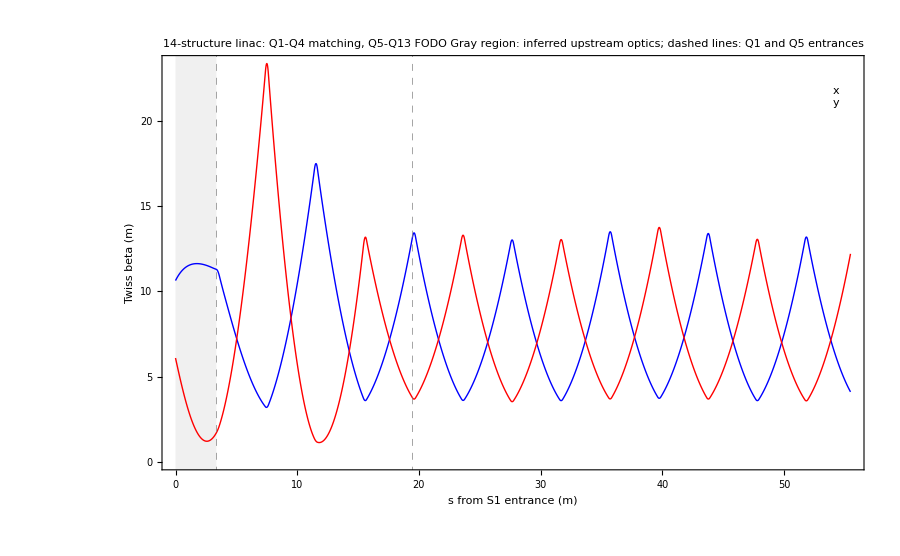

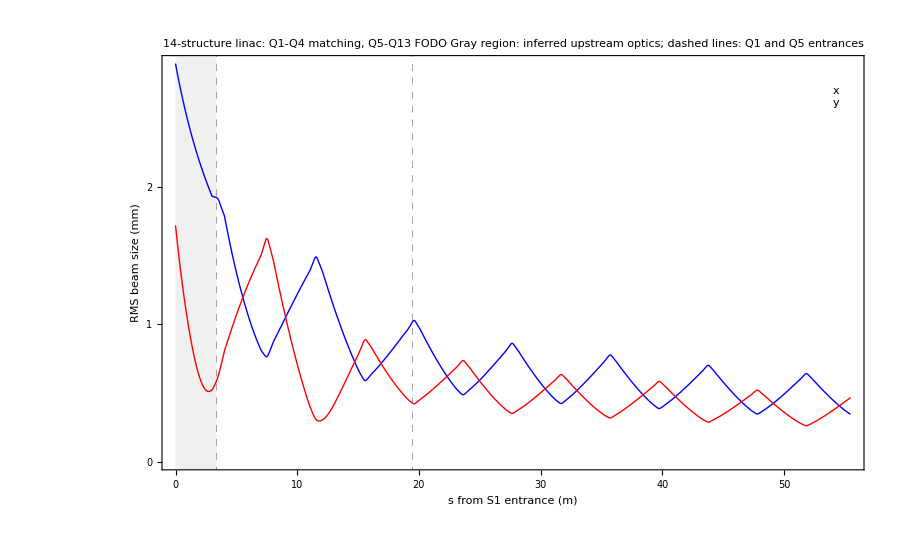

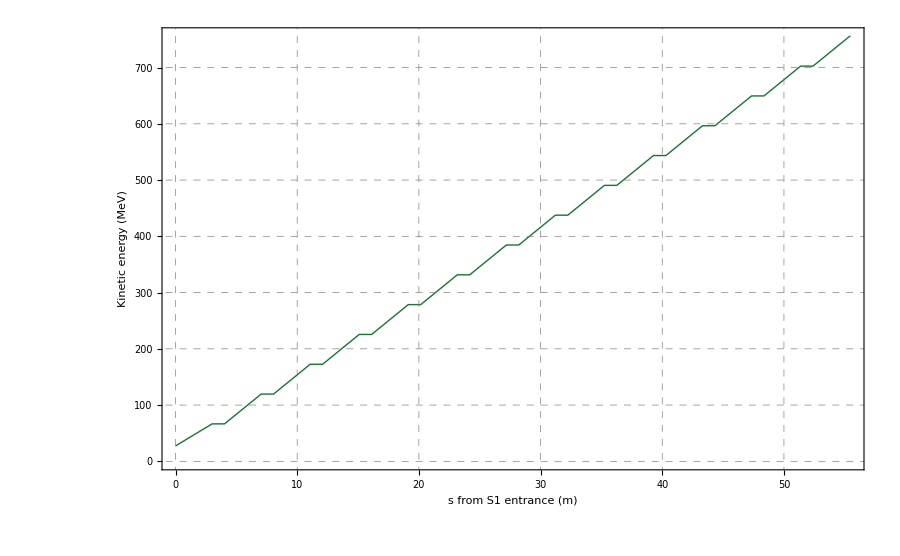

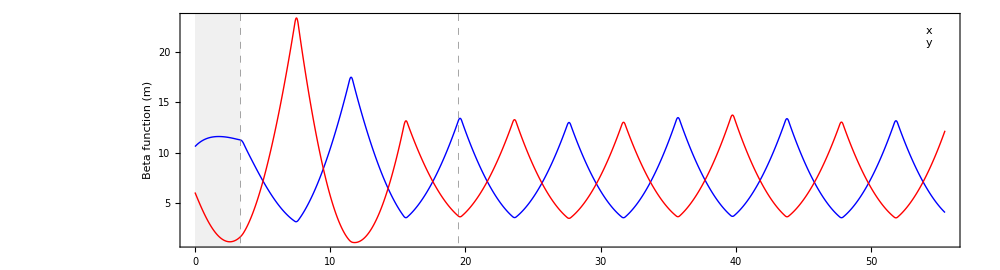
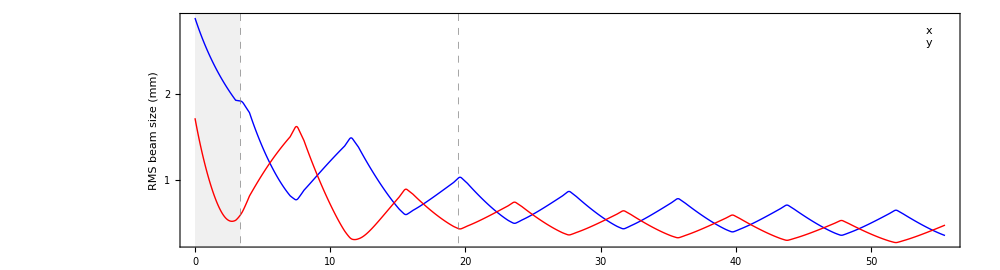
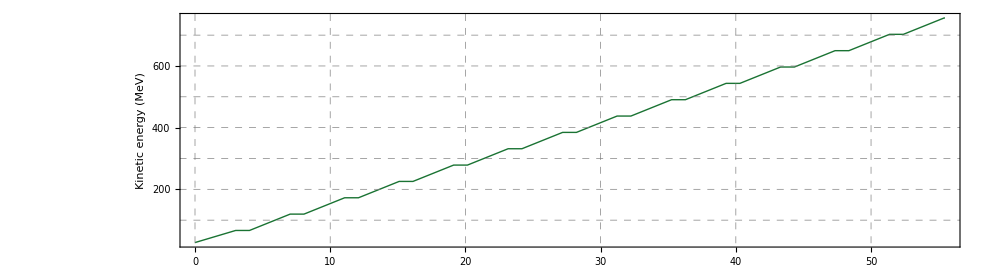
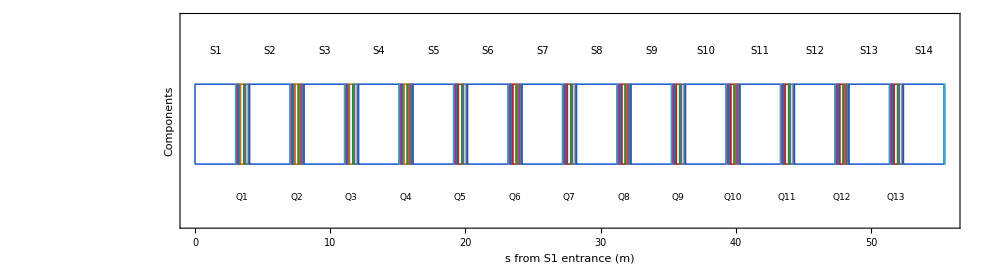
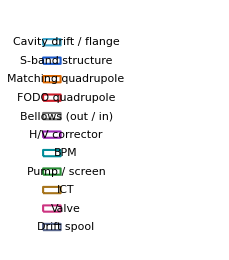
-Graphics- | 
-Graphics- | 
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
inputSigmaX = emitNxMMmrad 10^-6/(mom[energyAtQ1MeV]/me) inputTX;
inputSigmaY = emitNyMMmrad 10^-6/(mom[energyAtQ1MeV]/me) inputTY;
(* Reconstruct S1 upstream of the specified input point by inverse transport.
   It is inferred from Q1 inputs, not an independent upstream triplet solution. *)
upstream=Take[lattice,q1Index-1];
upstreamMap[plane_] := Fold[elementMatrix[#2,matchedK,plane].#1 &,IdentityMatrix[2],upstream];
startSigmaX=transport[Inverse[upstreamMap["x"]],inputSigmaX];
startSigmaY=transport[Inverse[upstreamMap["y"]],inputSigmaY];
data={}; sx=startSigmaX; sy=startSigmaY;
Do[
 steps=Switch[e["Type"],"RF",nRF,"Quad",nQuad,_,nDrift];
 Do[
  tx=transport[elementMatrix[e,matchedK,"x",z],sx];
  ty=transport[elementMatrix[e,matchedK,"y",z],sy];
  ek=e["Kin_MeV"]+(e["Kout_MeV"]-e["Kin_MeV"]) z/e["Length_m"];
  AppendTo[data,{e["sStart_m"]+z,unitTwiss[tx][[1,1]],unitTwiss[ty][[1,1]],
   1000 Sqrt[tx[[1,1]]],1000 Sqrt[ty[[1,1]]],ek,
   -unitTwiss[tx][[1,2]],-unitTwiss[ty][[1,2]],
   Sqrt[Det[tx]] mom[ek]/me 10^6,Sqrt[Det[ty]] mom[ek]/me 10^6}],
 {z,Subdivide[0.,e["Length_m"],steps]}];
 sx=transport[elementMatrix[e,matchedK,"x"],sx];
 sy=transport[elementMatrix[e,matchedK,"y"],sy],{e,lattice}];
makePlot[cols_,ylabel_] := ListLinePlot[(data[[All,{1,#}]]& /@ cols),
 PlotTheme->"Classic",Background->White,FrameStyle->Black,LabelStyle->Directive[Black,13],
 Frame->True,Axes->False,FrameLabel->{"s from S1 entrance (m)",ylabel},
 PlotLegends->None,
 FrameTicks->{{Table[{v,Style[NumberForm[v,{5,1}],Black,13]},
 {v,FindDivisions[{Min[data[[All,cols]]],Max[data[[All,cols]]]},5]}],None},
 {Table[{v,Style[v,Black,13]},{v,Range[0,50,10]}],None}},
 Epilog->Inset[Framed[Column[{Style["x",Blue,14],Style["y",Red,14]}],
 Background->White,FrameStyle->LightGray],Scaled[{.96,.9}]],PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},
 GridLines->{{sInput,sMatch},None},GridLinesStyle->Directive[Gray,Dashed],
 Prolog->{GrayLevel[.94],Rectangle[{0,-100000},{sInput,100000}]},
 PlotRange->All,ImageSize->900,
 PlotLabel->"14-structure linac: Q1-Q4 matching, Q5-Q13 FODO\nGray region: inferred upstream optics; dashed lines: Q1 and Q5 entrances",
 BaseStyle->{FontFamily->"Helvetica",FontSize->13}];
betaPlot=makePlot[{2,3},"Twiss beta (m)"];
beamSizePlot=makePlot[{4,5},"RMS beam size (mm)"];
(* Energy is kinetic energy; column 6 includes the gains inside each RF structure. *)
energyYTicks = Range[0,100 Ceiling[Max[data[[All,6]]]/100],100];
energyXTicks = FindDivisions[{0,position},6];
energyPlot=ListLinePlot[data[[All,{1,6}]],PlotTheme->"Classic",
 Background->White,Frame->True,Axes->False,FrameStyle->Black,
 LabelStyle->Directive[Black,13],FrameLabel->{"s from S1 entrance (m)","Kinetic energy (MeV)"},
 FrameTicks->{{Table[{v,Style[v,Black,13]},{v,energyYTicks}],None},
 {Table[{v,Style[v,Black,13]},{v,FindDivisions[{0,position},6]}],None}},
 GridLines->{energyXTicks,energyYTicks},
 GridLinesStyle->Directive[Gray,Dashed],
 PlotStyle->Directive[RGBColor[.1,.45,.2],Thick],PlotRange->All,ImageSize->900];

(* Four aligned rows; hollow boxes occupy the actual longitudinal component lengths. *)
componentStyles=<|
 "CavityExt"->{"Cavity drift / flange",RGBColor[.25,.65,.8]},
 "RF"->{"S-band structure",RGBColor[.1,.35,.8]},
 "MatchingQuad"->{"Matching quadrupole",RGBColor[.85,.4,0]},
 "FODOQuad"->{"FODO quadrupole",RGBColor[.8,.1,.15]},
 "Bellows"->{"Bellows (out / in)",RGBColor[.45,.45,.45]},
 "Corrector"->{"H/V corrector",RGBColor[.6,.15,.7]},
 "BPM"->{"BPM",RGBColor[0,.55,.6]},
 "ScreenPump"->{"Pump / screen",RGBColor[.15,.55,.2]},
 "ICT"->{"ICT",RGBColor[.65,.45,.1]},
 "Valve"->{"Valve",RGBColor[.8,.2,.5]},
 "Spool"->{"Drift spool",RGBColor[.35,.4,.55]}|>;
componentKey[e_] := Which[e["Type"]=="Quad",If[e["Index"]<=4,"MatchingQuad","FODOQuad"],
 StringStartsQ[e["Name"],"Bellow"],"Bellows",StringStartsQ[e["Name"],"Spool"],"Spool",True,e["Type"]];
commonPadding={{80,20},{45,25}};
commonXTicks=Table[{v,Style[v,Black,12]},{v,FindDivisions[{0,position},6]}];
componentPlot=Graphics[Table[With[{x=e["sStart_m"],y=e["sEnd_m"],key=componentKey[e]},
 {FaceForm[None],EdgeForm[Directive[componentStyles[key][[2]],AbsoluteThickness[1.1]]],
 Rectangle[{x,.2},{y,.8}],
 If[e["Type"]=="RF",{Black,Text[Style[e["Name"],10],{(x+y)/2,1.05}]},{}],
 If[e["Type"]=="Quad",{Black,Text[Style[e["Name"],9],{(x+y)/2,-.05}]},{}]}],{e,lattice}],
 Background->White,Frame->True,Axes->False,FrameStyle->Black,
 FrameTicks->{{None,None},{commonXTicks,None}},
 FrameLabel->{Style["s from S1 entrance (m)",Black,13],Style["Components",Black,13]},
 PlotRange->{{0,position},{-.25,1.3}},PlotRangePadding->None,
 ImagePadding->commonPadding,ImageSize->{1000,270},AspectRatio->Full];
componentLegend=Graphics[MapIndexed[Function[{entry,idx},With[{yy=Length[componentStyles]+1-First[idx]},
 {FaceForm[None],EdgeForm[Directive[entry[[2]],AbsoluteThickness[1.5]]],
 Rectangle[{0,yy-.17},{.8,yy+.17}],Black,
 Text[Style[entry[[1]],11],{1.05,yy},{-1,0}]}]],Values[componentStyles]],
 Background->White,PlotRange->{{-.15,7.6},{.5,Length[componentStyles]+1}},ImageSize->{230,260},ImagePadding->0];
stackPanel[g_,ylabel_,yticks_] := Show[g,PlotLabel->None,
 FrameLabel->{None,Style[ylabel,Black,13]},
 FrameTicks->{{yticks,None},{commonXTicks,None}},
 PlotRange->{{0,position},All},PlotRangePadding->{{0,0},{Scaled[.04],Scaled[.04]}},
 ImagePadding->commonPadding,ImageSize->{1000,270},AspectRatio->Full];
numberTicks[cols_] := Table[{v,Style[NumberForm[v,{5,1}],Black,12]},
 {v,FindDivisions[{Min[data[[All,cols]]],Max[data[[All,cols]]]},5]}];
betaPanel=stackPanel[betaPlot,"Beta function (m)",numberTicks[{2,3}]];
sizePanel=stackPanel[beamSizePlot,"RMS beam size (mm)",numberTicks[{4,5}]];
energyPanel=stackPanel[energyPlot,"Kinetic energy (MeV)",
 Table[{v,Style[v,Black,12]},{v,energyYTicks}]];
layoutPlot=Grid[{{betaPanel,Spacer[{230,1}]},{sizePanel,Spacer[{230,1}]},
 {energyPanel,Spacer[{230,1}]},{componentPlot,componentLegend}},
 Spacings->{0,0},Alignment->{Left,Center},Background->White];
If[$FrontEnd =!= Null, Print[betaPlot];Print[beamSizePlot];Print[energyPlot];Print[layoutPlot]];
```

## 7. Strength table, portable lattice, optics and figures

```mathematica
quadTable=Table[With[{e=quadElements[[j]],k=matchedK[[j]]},
 <|"Quad"->e["Name"],"Role"->If[j<=4,"Matching",If[k>0,"F","D"]],
 "sEntrance_m"->e["sStart_m"],"sCenter_m"->(e["sStart_m"]+quadLength/2),
 "KineticEnergy_MeV"->e["Kin_MeV"],"EffectiveLength_m"->quadLength,
 "k_m^-2"->k,"kL_m^-1"->k quadLength,"Gradient_T_per_m"->k brho[e["Kin_MeV"]],"Gradient_Gauss_per_cm"->100 k brho[e["Kin_MeV"]]|>],{j,13}];
Print[Dataset[KeyTake[#, {"Quad", "Role", "Gradient_Gauss_per_cm"}] & /@ quadTable]];
exportLattice=Map[Function[e,Join[e,<|"k_m^-2"->If[e["Type"]=="Quad",matchedK[[e["Index"]]],0.],
 "Gradient_T_per_m"->If[e["Type"]=="Quad",matchedK[[e["Index"]]] brho[e["Kin_MeV"]],0.],
 "RFPhase_deg"->If[e["Type"]=="RF",rfPhaseDeg,0.]|>]],lattice];
If[!DirectoryQ[outputDirectory],CreateDirectory[outputDirectory]];
exportCSV[name_,rows_] := Export[FileNameJoin[{outputDirectory,name}],Prepend[Values /@ rows,Keys[First[rows]]],"CSV"];
exportCSV["quadrupoles.csv",quadTable]; exportCSV["lattice.csv",exportLattice];
Export[FileNameJoin[{outputDirectory,"optics.csv"}],Prepend[data,
 {"s_m","beta_x_m","beta_y_m","sigma_x_mm","sigma_y_mm","KineticEnergy_MeV",
 "alpha_x","alpha_y","emit_nx_mm_mrad","emit_ny_mm_mrad"}],"CSV"];
Put[<|"Description"->"Sband14 uncoupled linear lattice; RF map defined in Sband14_Matching.wl",
 "Elements"->exportLattice,"QuadSettings"->quadTable,"InputPoint_m"->sInput,
 "InputTwiss"->{betaXIn,alphaXIn,betaYIn,alphaYIn},"MatchingPlane_m"->sMatch,
 "TargetTwissX"->targetX,"TargetTwissY"->targetY,"Residual"->matchResidual,
 "ReferencePhasePerFullCell_deg"->phasePerFullCellDeg|>,FileNameJoin[{outputDirectory,"Sband14_lattice.wl"}]];
Do[Export[FileNameJoin[{outputDirectory,item[[1]]<>".pdf"}],item[[2]]];
 Export[FileNameJoin[{outputDirectory,item[[1]]<>".png"}],item[[2]],ImageResolution->180],
 {item,{{"beta_functions",betaPlot},{"beam_sizes",beamSizePlot},{"kinetic_energy",energyPlot},{"layout",layoutPlot}}}];
Print["Outputs written to ",outputDirectory];
```

Outputs written to /Users/wange/Documents/Research/eRHIC injector/eRHIC baseline/Beamline/physics/Sband14_output